### Start choosing the example:

```mathematica
t=14;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15,S1->0, S2->0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.192499 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.245024,Null}

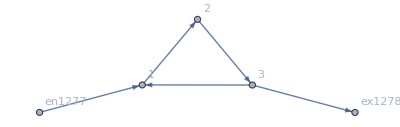

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1279→26.6667,j1280→26.6667,j1281→0,j1282→80.,j1283→80.,j1284→0,j1285→0.,j1286→53.3333,j1287→0.,j1288→0.,jt1289→0.,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→26.6667,jt1294→53.3333,jt1295→26.6667,jt1296→0.,jt1297→0.,jt1298→26.6667,jt1299→0.,jt1300→53.3333,jt1301→0.,jt1302→0.,u1303→68.3333,u1304→41.6667,u1305→15.,u1306→15.,u1307→68.3333,u1308→41.6667,u1309→15.,u1310→68.3333,u1311→15.,u1312→68.3333|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0179586

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0177279

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0174905

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0172467

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0169969

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0167415

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0164808

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0162152

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.015945

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0156705

<|j1279→20.5557,j1280→20.5557,j1281→0,j1282→80.,j1283→80.,j1284→0,j1285→0.,j1286→59.4443,j1287→0.,j1288→0.,jt1289→0.,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→20.5557,jt1294→59.4443,jt1295→20.5557,jt1296→0.,jt1297→0.,jt1298→20.5557,jt1299→0.,jt1300→59.4443,jt1301→0.,jt1302→0.,u1303→18.0523,u1304→16.5261,u1305→15.,u1306→15.,u1307→18.0523,u1308→16.5261,u1309→15.,u1310→18.0523,u1311→15.,u1312→18.0523|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0201858

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0198039

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0194149

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0190197

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.018619

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0182136

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0178043

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0173918

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0169767

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0165597

<|j1279→20.0153,j1280→20.0153,j1281→0,j1282→80.,j1283→80.,j1284→0,j1285→0.,j1286→59.9847,j1287→0.,j1288→0.,jt1289→0.,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→20.0153,jt1294→59.9847,jt1295→20.0153,jt1296→0.,jt1297→0.,jt1298→20.0153,jt1299→0.,jt1300→59.9847,jt1301→0.,jt1302→0.,u1303→18.6027,u1304→16.8013,u1305→15.,u1306→15.,u1307→18.6027,u1308→16.8013,u1309→15.,u1310→18.6027,u1311→15.,u1312→18.6027|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0259476

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0249064

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0238756

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0228586

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0218582

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0208768

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0199166

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0189794

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0180665

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0171791

<|j1279→18.9805,j1280→18.9805,j1281→0,j1282→80.,j1283→80.,j1284→0,j1285→0.,j1286→61.0195,j1287→0.,j1288→0.,jt1289→0.,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→18.9805,jt1294→61.0195,jt1295→18.9805,jt1296→0.,jt1297→0.,jt1298→18.9805,jt1299→0.,jt1300→61.0195,jt1301→0.,jt1302→0.,u1303→20.261,u1304→17.6305,u1305→15.,u1306→15.,u1307→20.261,u1308→17.6305,u1309→15.,u1310→20.261,u1311→15.,u1312→20.261|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0369234

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0166028

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00746454

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.003356

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00150885

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000678377

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000304999

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000137128

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000616529

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000277193

<|j1279→24.5232,j1280→24.5232,j1281→0,j1282→80.,j1283→80.,j1284→0,j1285→0.,j1286→55.4768,j1287→0.,j1288→0.,jt1289→0.,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→24.5232,jt1294→55.4768,jt1295→24.5232,jt1296→0.,jt1297→0.,jt1298→24.5232,jt1299→0.,jt1300→55.4768,jt1301→0.,jt1302→0.,u1303→48.009,u1304→31.5045,u1305→15.,u1306→15.,u1307→48.009,u1308→31.5045,u1309→15.,u1310→48.009,u1311→15.,u1312→48.009|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.68439×10^-14

<|j1279→26.6667,j1280→26.6667,j1281→0,j1282→80.,j1283→80.,j1284→0,j1285→0.,j1286→53.3333,j1287→0.,j1288→0.,jt1289→0.,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→26.6667,jt1294→53.3333,jt1295→26.6667,jt1296→0.,jt1297→0.,jt1298→26.6667,jt1299→0.,jt1300→53.3333,jt1301→0.,jt1302→0.,u1303→68.3333,u1304→41.6667,u1305→15.,u1306→15.,u1307→68.3333,u1308→41.6667,u1309→15.,u1310→68.3333,u1311→15.,u1312→68.3333|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.617897

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.929008

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.13378

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.0854

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.02683

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00474

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00036

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→2.84967×10^23,j1285→2.84967×10^23,j1286→2.84967×10^23,j1287→0.,j1288→0.,jt1289→2.84967×10^23,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→2.84967×10^23,jt1297→0.,jt1298→0.,jt1299→2.84967×10^23,jt1300→80.,jt1301→0.,jt1302→0.,u1303→4.02653×10^8,u1304→2.01327×10^8,u1305→15.,u1306→15.,u1307→4.36208×10^8,u1308→2.01327×10^8,u1309→15.,u1310→4.36208×10^8,u1311→15.,u1312→4.36208×10^8|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«6 more identical outputs»

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→1.25521×10^189,j1285→1.25521×10^189,j1286→1.25521×10^189,j1287→0.,j1288→0.,jt1289→1.25521×10^189,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→1.25521×10^189,jt1297→0.,jt1298→0.,jt1299→1.25521×10^189,jt1300→80.,jt1301→0.,jt1302→0.,u1303→0.,u1304→0.,u1305→15.,u1306→15.,u1307→0.,u1308→0.,u1309→15.,u1310→0.,u1311→15.,u1312→0.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«7 more identical outputs»

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→1.23536349271862×10^859,j1285→1.23536349271862×10^859,j1286→1.23536349271862×10^859,j1287→0.,j1288→0.,jt1289→1.23536349271862×10^859,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→1.23536349271862×10^859,jt1297→0.,jt1298→0.,jt1299→1.23536349271862×10^859,jt1300→80.,jt1301→0.,jt1302→0.,u1303→0``-843.7392649841213,u1304→0``-843.4382349884572,u1305→15.,u1306→15.,u1307→0``-843.4382349884572,u1308→0``-843.4382349884572,u1309→15.,u1310→0``-843.4382349884572,u1311→15.,u1312→0.|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«17 more identical outputs»

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→5.25227×10^47,j1285→5.25227×10^47,j1286→5.25227×10^47,j1287→0.,j1288→0.,jt1289→5.25227×10^47,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→5.25227×10^47,jt1297→0.,jt1298→0.,jt1299→5.25227×10^47,jt1300→80.,jt1301→0.,jt1302→0.,u1303→0.,u1304→0.,u1305→15.,u1306→15.,u1307→0.,u1308→0.,u1309→15.,u1310→0.,u1311→15.,u1312→0.|>